```mathematica
SurfacePositions = Select[ Flatten[Table[{i,j,k},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],2], (#[[1]]==1 ||#[[1]]==dim[[1]] ||#[[2]]==1 ||#[[2]]==dim[[2]]||#[[3]]==1 ||#[[3]]==dim[[3]] )&];
```

```mathematica
Fibers = Round[FiberData];
Fibers = Select[Fibers,MemberQ[SurfacePositions,Last[#]]&];
```

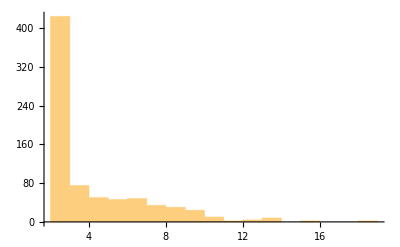

```mathematica
Histogram[Table[Length[Fibers[[i]]],{i,1,Length[Fibers]}]]
```

```mathematica
ConnectivityMatrix[]:=Module[{N=Length[SurfacePositions],CM,CleanFibers,i,j},

CleanFibers = Select[Fibers,Length[#]>1&];
CM = Table[0,{i,1,N},{j,1,N}];

Table[
i=Position[SurfacePositions,First[fiber]][[1,1]];
j=Position[SurfacePositions,Last[fiber]][[1,1]];
CM[[i,j]] = 1;
CM[[j,i]] = 1;
,{fiber,CleanFibers}];

CM
]
```

```mathematica
ConnectivityMatrix[]:=Module[{N=Length[SurfacePositions],CM,CleanFibers,i,j,con1,con2,con11,con22,dist},

CleanFibers = Select[Fibers,Length[#]>1&];
CM = Table[0,{i,1,N},{j,1,N}];

Table[
i=Position[SurfacePositions,v1][[1,1]];
j=Position[SurfacePositions,v2][[1,1]];
con11 = Join[Select[CleanFibers,First[#]==v1&],Reverse[Select[CleanFibers,Last[#]==v1&],2]];
con22 =  Join[Select[CleanFibers,First[#]==v2&],Reverse[Select[CleanFibers,Last[#]==v2&],2]];
con1 = Table[Last[con11[[i]]],{i,1,Length[con11]}];
con2 = Table[Last[con22[[i]]],{i,1,Length[con22]}];

dist=Min[Table[Max[Abs[c1-c2]],{c1,con1},{c2,con2}]];

If[Max[Abs[v1-v2]]≤1&&dist≤1&&i≠j,
CM[[i,j]] = 1;
CM[[j,i]] = 1;
]
,{v1,SurfacePositions},{v2,SurfacePositions}];

CM
]
```

```mathematica
CM =ConnectivityMatrix[];
```

```mathematica
ArrayPlot[CM,ColorFunction->"Monochrome"]
```

-Graphics-

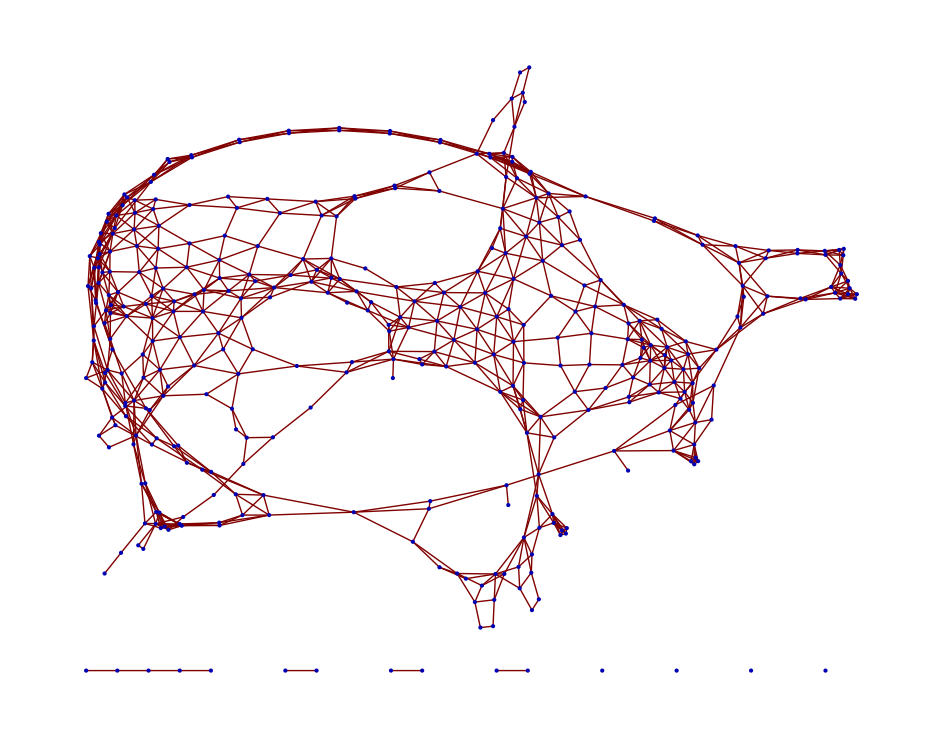

```mathematica
GraphPlot[CM]
```

```mathematica
CommunityGraphPlot[g,FindGraphCommunities[g]]
```

-Graphics-

```mathematica
Module[{g,partitions},
g=AdjacencyGraph[CM];
partitions =FindGraphCommunities[g];
partitions =Select[partitions,Length[#]>2&];

Graphics3D[Flatten[Table[Table[
{ColorData["DarkBands"][(i-1)/10],Sphere[SurfacePositions[[j]]]}
,{j,partitions[[i]]}],{i,1,Length[partitions]}],1]]
]
```

```mathematica
Graphics3D[
Table[v1[i,j,k],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]],1}]]
```